```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
diffFunc[ arr_ ]:=Table[Subtract[arr⟦i⟧,arr⟦i-1⟧] , {i,2,Length[arr],1}];
```

```mathematica
osxdata=Flatten[Import["osx_macair_2013.csv"]];
```

```mathematica
ListPlot[osxdata]
```

-Graphics-

```mathematica
diffosxdata=diffFunc[osxdata];
```

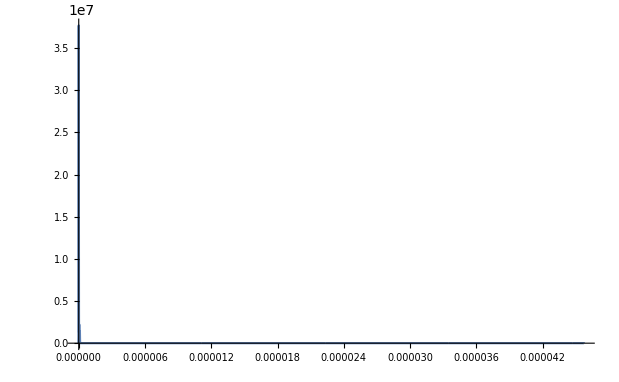

```mathematica
SmoothHistogram[diffosxdata,PlotRange->Full]
```

```mathematica
linuxdata = Flatten[Import["linux_intelE3_2011.csv"]];
```

-Graphics-

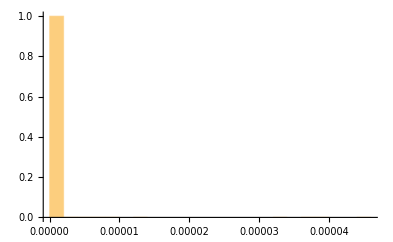

```mathematica
ListPlot[linuxdata]
linuxdiff = diffFunc[linuxdata];
Histogram[linuxdiff, Automatic,"Probability"]
```